```mathematica
Clear[a,b,c,a1,c1,d1,d2,d3,d4]

For[a=1.0;b=2.0;i=1,

i≤20,d1[i]=a;d2[i]=b;c=(a+b)/2;d3[i]=c;
f[x_]=x^3-x-1; c1=f[c];d4[i]=c1;a1=f[a];
If[a1*c1<0,b=c,a=c;a1=c1];i++]
lst=Table[{i,d1[i],d2[i],d3[i],d4[i]},{i,1,20}];
TableForm[lst,TableHeadings->{None,{"iter","a","b","c","f(c)"}}]
Print["One of the real root of the given equation is = ",c]
```

iter | a | b | c | f(c)
1 | 1. | 2. | 1.5 | 0.875
2 | 1. | 1.5 | 1.25 | -0.296875
3 | 1.25 | 1.5 | 1.375 | 0.224609
4 | 1.25 | 1.375 | 1.3125 | -0.0515137
5 | 1.3125 | 1.375 | 1.34375 | 0.0826111
6 | 1.3125 | 1.34375 | 1.32813 | 0.014576
7 | 1.3125 | 1.32813 | 1.32031 | -0.0187106
8 | 1.32031 | 1.32813 | 1.32422 | -0.00212795
9 | 1.32422 | 1.32813 | 1.32617 | 0.00620883
10 | 1.32422 | 1.32617 | 1.3252 | 0.00203665
11 | 1.32422 | 1.3252 | 1.32471 | -0.0000465949
12 | 1.32471 | 1.3252 | 1.32495 | 0.000994791
13 | 1.32471 | 1.32495 | 1.32483 | 0.000474039
14 | 1.32471 | 1.32483 | 1.32477 | 0.000213707
15 | 1.32471 | 1.32477 | 1.32474 | 0.0000835524
16 | 1.32471 | 1.32474 | 1.32472 | 0.0000184779
17 | 1.32471 | 1.32472 | 1.32471 | -0.0000140587
18 | 1.32471 | 1.32472 | 1.32472 | 2.20949×10^-6
19 | 1.32471 | 1.32472 | 1.32472 | -5.92464×10^-6
20 | 1.32472 | 1.32472 | 1.32472 | -1.85758×10^-6

One of the real root of the given equation is = 1.32472

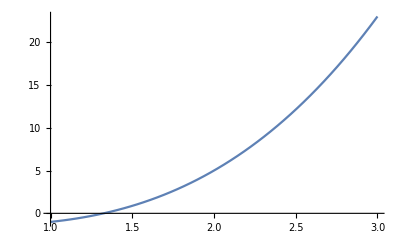

```mathematica
Plot[f[x],{x,1,3}]
```